```mathematica
datFileLocalChernlocation="/data/topo_super/weak_invariant/";
```

```mathematica
datfileOBCNameIrrat="t0=1_t=1_m_0=-0.2_mu=1.2_Delta=0.5_ky=0_x_periodic=0_y_periodic=0_L=84_m=0.6180339887498949_c1=6_c2=18";
```

```mathematica
datfileOBCNamekyPiIrrat="t0=1_t=1_m_0=-0.2_mu=1.2_Delta=0.5_ky=π_x_periodic=0_y_periodic=0_L=84_m=0.6180339887498949_c1=6_c2=18";
```

```mathematica
datfileOBCNameTrivialIrrat="t0=1_t=1_m_0=-0.2_mu=1.2_Delta=2.5_x_periodic=0_y_periodic=0_L=84_m=0.6180339887498949_c1=6_c2=18";
```

```mathematica
datfileOBCNameRat="t0=1_t=1_m_0=-0.2_mu=1.2_Delta=0.5_ky=0_x_periodic=0_y_periodic=0_L=84_m=0.6666666666666666_c1=6_c2=18";
```

```mathematica
datfileOBCNamekyPiRat="t0=1_t=1_m_0=-0.2_mu=1.2_Delta=0.5_ky=π_x_periodic=0_y_periodic=0_L=84_m=0.6666666666666666_c1=6_c2=18";
```

```mathematica
datfileOBCNameTrivialRat="t0=1_t=1_m_0=-0.2_mu=1.2_Delta=2.5_x_periodic=0_y_periodic=0_L=84_m=0.6666666666666666_c1=6_c2=18";
```

```mathematica
list0=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNameIrrat,".csv"]]];
```

```mathematica
list0Pi=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNamekyPiIrrat,".csv"]]];
```

```mathematica
list0Trivial=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNameTrivialIrrat,".csv"]]];
```

Import::nffil: File /home/archisman/Documents/GitHub/lattices-julia/data/topo_super/weak_invariant/t0=1_t=1_m_0=-0.2_mu=1.2_Delta=2.5_x_periodic=0_y_periodic=0_L=84_m=0.6180339887498949_c1=6_c2=18.csv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
list1=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNameRat,".csv"]]];
```

```mathematica
list1Pi=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNamekyPiRat,".csv"]]];
```

```mathematica
list1Trivial=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,datfileOBCNameTrivialRat,".csv"]]];
```

Import::nffil: File /home/archisman/Documents/GitHub/lattices-julia/data/topo_super/weak_invariant/t0=1_t=1_m_0=-0.2_mu=1.2_Delta=2.5_x_periodic=0_y_periodic=0_L=84_m=0.6666666666666666_c1=6_c2=18.csv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
Lx=Dimensions[list1][[1]]
```

84

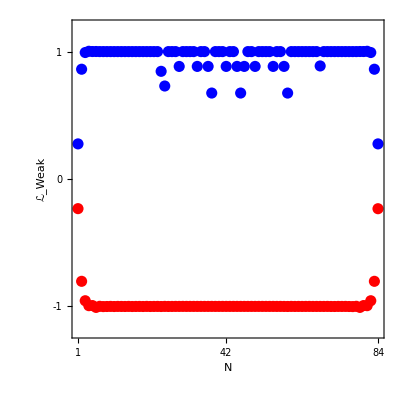

```mathematica
Show[ListPlot[list0,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list0Pi,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-2,"-2"},{-1,"-1"},{0,"0"},{1,"1"},{2,"2"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","ℒ_Weak"},RotateLabel->False]
```

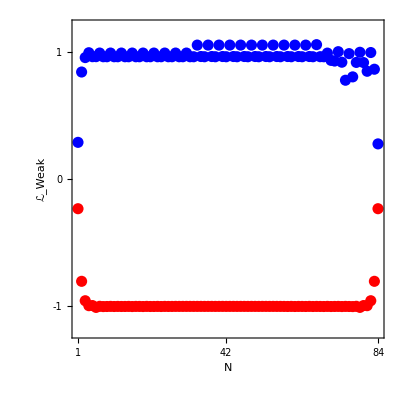

```mathematica
Show[ListPlot[list1,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list1Pi,PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-2,"-2"},{-1,"-1"},{0,"0"},{1,"1"},{2,"2"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","ℒ_Weak"},RotateLabel->False]
```